```mathematica
SOI=Import["/users/pp/github/context/Mathematica/SOIM/data/soi.txt", "table"];
TSID=Import["/users/pp/github/context/Mathematica/SOIM/data/tsi.txt", "table"];
QBO=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo20.txt", "table"];
QBO70=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo.txt", "table"];
CW=Import["/users/pp/github/context/Mathematica/SOIM/data/cw.txt", "table"];
CW1=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1_1930.txt", "table"];
CW0=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1.txt", "table"];
NINO34=Import["/users/pp/github/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
tahiti=Import["/users/pp/github/context/Mathematica/SOIM/data/tahiti.txt", "table"];
darwin=Import["/users/pp/github/context/Mathematica/SOIM/data/darwin0.txt", "table"];
noi=Import["/users/pp/github/context/Mathematica/SOIM/data/noi.txt", "table"];
```

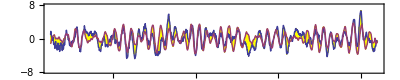

{4.03898 = char t,0.771058 =err,1881.  .. ,1980.,CC,53.79,53.79,0.}

{4.03898 = char t,-0.0318643 =err,1881.  .. ,1980.,CC,68.786,68.786,0.}

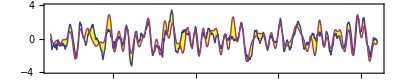

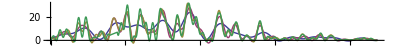

2.90888

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;  CF = 2.42;
(* STRT=220; LNGTH=300; *)
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
qbo[x_]:= 1.13*Cos[2*Pi/2.3333*x-0.23*Cos[2*Pi*x-0.4]+0.5*Cos[2*Pi/18.63*x+1.4]-1.4]+ 0.53*Cos[2*Pi/2.239*x+0.3];  (* 0.99 *)
RHS[x_]:= qbo[x] -   0.91*Cos[2*Pi/2.902*x+0.4] ;  (* 0.99 *)
       (* 0.32*Cos[2*Pi/2.94*x+1.95]; *) (* 0.99 *)
rhs=Table[{1880.0+x,  -1.5*If[x>99.3 && x<121,-1,1]*RHS[x-0.01]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    
              PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] *)
Window := 5;
R = (1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
  TR=52.0;  SHFT=-1.17;
OSC := 9.305;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.6*Cos[2*Pi/OSC*x+3.3] +0.4*Cos[2*Pi/(2*OSC)*x+4.2]  );
Semidiurnal[x_] := 1.2*Cos[2*Pi*x/(SEMI)-1.3]-0*0.8*Cos[2*Pi*x/(SEMI/2)+0.1];
Tides[x_] := +1.4*Diurnal[x] + 0*.4*Semidiurnal[x];
SOLN=NDSolve[{y''[x]+CF*y[x] ==4.8*RHS[x+0.05] - 1.8*Cos[2*Pi/6.46*x-0.6] + 0.6*Cos[2*Pi/5.78*x+0.1]+ 0.9*Cos[2*Pi/7.33*x+1.8] +1.2*Tides[x], 
                               y'[TR]==4.1, y[TR]==-0.4}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.64*(0.99*Cos[2*Pi/2.905*x+1.7]+First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIM[[All,2]]-SOIT[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.18/12
```

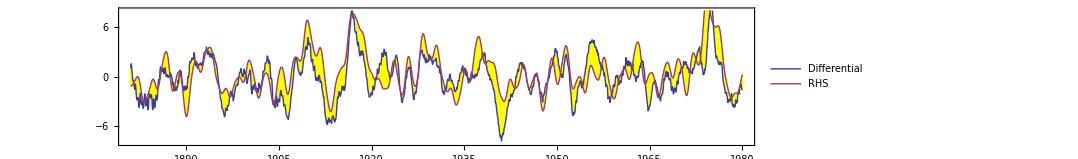

{3.18161 = char t,-0.223674 =err,1881.  .. ,1980.,CC,73.8378,68.1208,-5.71694}

{3.18161 = char t,0.230356 =err,1881.  .. ,1980.,CC,-6.01432,-5.83978,0.174541}

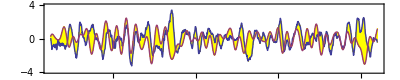

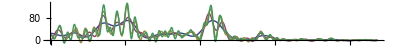

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;  CF =3.9; Hill = 0.0*1.19986;
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
N1=9.20892; nine[x_] := 3.13684*Cos[2*Pi/N1*x+4.94]+0.1*Cos[2*Pi/9*x+4.3]+1.0501*Cos[2*Pi/(3*N1)*x+4.0738];
Q1=2.3069; qbo[x_] := 0.97374*Cos[2*Pi/(3*Q1)*x+5.63]+2.62983*Cos[2*Pi/Q1*x+0.38*Sin[2*Pi/18.5797*x+0.21]+
                      0.37*Sin[2*Pi/9.29845*x+0.3]+0.94306]+1.007*Cos[2*Pi/2.07671*x+5.27978]+1.16459*Cos[2*Pi/2.86455*x+0.08288];
D1=8.84267; di[x_] := 0.66984*Cos[2*Pi*x/D1+5.75834];    lw[x_] := 2.311*Cos[2*Pi*x/65.9867+2.86145];
cw[x_] := 2.31607*Cos[2*Pi/6.41716*x+7.1121]+0.017*Cos[2*Pi/31*x+4]+1.44779*Cos[2*Pi/5.81*x+4.59627];
T1=22.0246; tsi[x_] := (1.9185*Cos[2*Pi*x/(T1/3)+6.69]+1.2518*Cos[2*Pi/T1*x+3.46422]+2.23755*Cos[2*Pi/(T1/2)*x+3.648])*
                       (1+0.00333*x) + 0.024*x;
eight[x_] := 1.15692*Cos[2*Pi/8*x+1.26296]; cw0[x_] := 0.4*Cos[2*Pi/1.1755*x+0.65];
RHS[x_]:= nine[x]+qbo[x]+di[x]+lw[x]+cw[x]+tsi[x]+eight[x]+cw0[x];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-(CF+Hill*tsi[x*12])*R[[x*12]] + 0.0*(R[[x*12]])^2},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  0.52*If[x>100.0,-1,1]*RHS[x-0.12]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] *)
Window := 5;   TR=52.0;  SHFT=-1.17;
R = (1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
SOLN=NDSolve[{y''[x]+(CF+Hill*tsi[x])*y[x] ==4.8*RHS[x],        y'[TR]==4.1, y[TR]==-0.4}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, -0.1*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIM[[All,2]]-SOIT[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
```

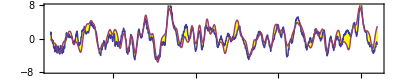

{3.26207 = char t,0.345036 =err,1881.  .. ,1980.,CC,81.8502,81.8511,0.000868833}

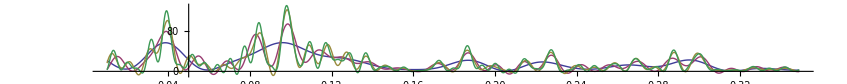

7.93331

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;  CF =3.71; Hill = 0.0*1.19986;
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
N1=9.206; nine[x_] := 3.1*Cos[2*Pi/N1*x+4.94]+0.1*Cos[2*Pi/9*x+4.3]+1.7*Cos[2*Pi/(3*N1)*x+2.8];
Q1=2.315; qbo[x_] := 0.98*Cos[2*Pi/(3*Q1)*x+6.]+2.0*Cos[2*Pi/Q1*x+0.3*Sin[2*Pi/9.29845*x+0.3]+1.0]+0.8*Cos[2*Pi/2.07671*x+5.4]+0.9*Cos[2*Pi/2.86455*x+0.08288]-1.1*Sin[2*Pi/2.24*x+2.2];
D1=8.84267; di[x_] := 0.66984*Cos[2*Pi*x/D1+5.75834];    lw[x_] := 2.311*Cos[2*Pi*x/66+2.9];
cw[x_] := 2.4*Cos[2*Pi/6.39*x+7.1121]+1.45*Cos[2*Pi/5.73*x+4.59627];
T1=22.0246; tsi[x_] := (1.92*Cos[2*Pi*x/(T1/3)+6.7]+1.2*Cos[2*Pi/T1*x+3.46422]+1.3*Cos[2*Pi/(T1/2)*x+4])*
                       (1+0*.00333*x) + 0.017*x;
eight[x_] := 1.5*Cos[2*Pi/7.95*x+1.6]; cw0[x_] := 0.3*Cos[2*Pi/1.1755*x-0.7];
RHS[x_]:= 0.9*nine[x]+0.9*qbo[x-0.05]+0.9*di[x]+0.41*lw[x]+1.1*cw[x]+1*tsi[x]+0.6*eight[x]+cw0[x];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-(CF+Hill*tsi[x*12])*R[[x*12]] + 0.4*(R[[x*12]])^2},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  0.58*If[x>100.0,-1,1]*RHS[x-0.18]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0.01,π/9},PlotRange->All,AspectRatio->0.1] 
2*Pi/.066/12
(* Window := 5;   TR=52.0;  SHFT=-1.17;
R = (1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
SOLN=NDSolve[{y''[x]+(CF+Hill*tsi[x])*y[x] ==4.8*RHS[x],        y'[TR]==4.1, y[TR]==-0.4}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, -0.1*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIM[[All,2]]-SOIT[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
```

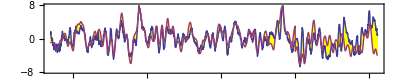

{3.58018 = char t,-0.459943 =err,1881.  .. ,1980.,CC,63.1502,63.4193,0.269153}

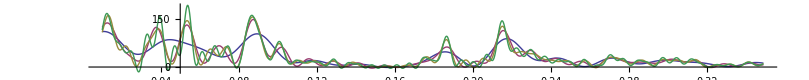

2.7851

```mathematica
Window = 7; 
STRT=12; LNGTH=1600;  CF =3.08; Hill = 0.0*1.19986;
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
N1=9.206; nine[x_] := 3.1*Cos[2*Pi/N1*x+4.94]+0.1*Cos[2*Pi/9*x+4.3]+1.7*Cos[2*Pi/(3*N1)*x+2.8];
Q1=2.315; qbo[x_] := 0.98*Cos[2*Pi/(3*Q1)*x+6.]+2.0*Cos[2*Pi/Q1*x+0.3*Sin[2*Pi/9.29845*x+0.3]+1.0]+0.8*Cos[2*Pi/2.07671*x+5.4]+
        0.9*Cos[2*Pi/2.864*x+0.0]-1.1*Sin[2*Pi/2.24*x+2.2];
D1=8.84267; di[x_] := 0.66984*Cos[2*Pi*x/D1+5.75834];    lw[x_] := 2.311*Cos[2*Pi*x/66+2.9];
cw[x_] := 2.05*Cos[2*Pi/6.41*x+1.18]+1.45*Cos[2*Pi/5.73*x+4.59627];
T1=22.0246; tsi[x_] := (1.92*Cos[2*Pi*x/(T1/3)+6.7]+1.2*Cos[2*Pi/T1*x+3.46422]+1.3*Cos[2*Pi/(T1/2)*x+4])*
                       (1+0*.00333*x) + 0.017*x;
eight[x_] := 1.5*Cos[2*Pi/8.0*x+2.0]; cw0[x_] := 0.3*Cos[2*Pi/1.1755*x-0.7];
RHS[x_]:= 0.9*nine[x]+0.9*qbo[x-0.05]+0.9*di[x]+0.41*lw[x]+1.1*cw[x]+1*tsi[x]+0.8*eight[x]+cw0[x];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-(CF+Hill*tsi[x*12])*R[[x*12]] + 0.4*(R[[x*12]])^2},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  0.58*If[x>100.0,-1,1]*RHS[x-0.18]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0.01,π/9},PlotRange->All,AspectRatio->0.1] 
2*Pi/.188/12
```